NotebookEvaluate::nbnfnd: Unable to find the notebook "C:\\Users\\Houman\\Documents\\plot_style.nb".

C:\Users\Houman\Documents\plot_style.nb

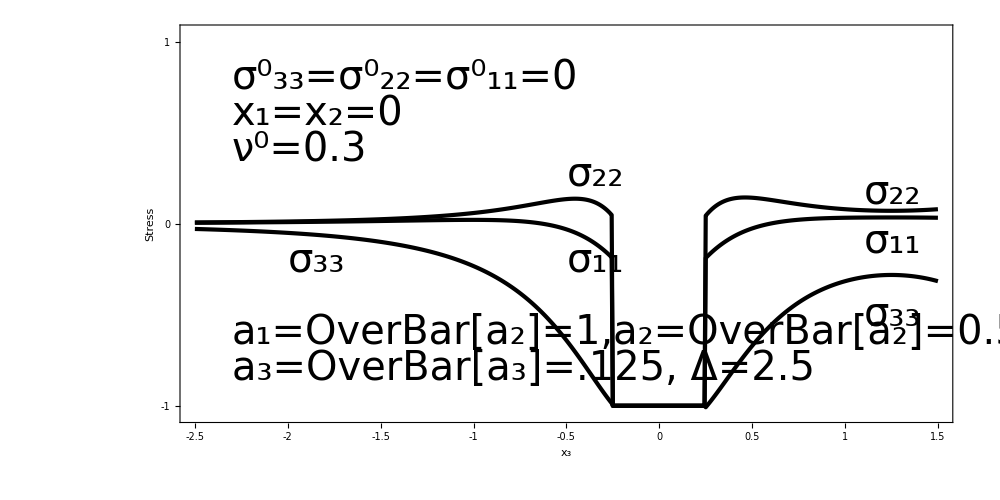

```mathematica
Clear["Global`*"];

(*---------------------------------------------------------------------------------------------------------*)
fileaddress=Directory[]<>"\\plot_style.nb";
NotebookEvaluate[fileaddress(*,InsertResults->True*)];
Print[fileaddress];

(*---------------------------------------------------------------------------------------------------------*)


SetDirectory[NotebookDirectory[]];
Get["plot_style.mx"];
Get["input_report.mx"];



Clear[i];
m[i_]=fr[xp1[i],xp2[i],xp3[i]];
Get["Fig4.mx"];
data[33]=Table[{m[k][[3]],m[k][[6]]},{k,1,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)

data[22]=Table[{m[k][[3]],m[k][[5]]},{k,1,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)

data[11]=Table[{m[k][[3]],m[k][[4]]},{k,1,howmany+1,1}];(*x[1],σ[33]*)




imgSize=1000;

fsmehvarx=40/1000*imgSize; (*font size x axis*)
fsmehvary=40/1000*imgSize ;     (*font size y axis*)

dataseries={data[33],data[22],data[11]};





figure=Show[{ListPlot[dataseries
,PlotStyle->{{Black,Bold,Thickness[.003/1000*imgSize]}}
,Joined->{True}

,AxesStyle->Large
,PlotRange->{{-2.5,1.5},{-1.05,1.05}}
(*,PlotRange->All*)
(*,Ticks->{{0,.2,.4,.6,.8,1},{0,.25,.50,.75,1}}*)
(*,TicksStyle->Directive[60]*)
(*,GridLines->{{1},{-1,1}}*)
(*,GridLines->{None,None}*)

,AspectRatio->10/20
,LabelStyle->{(*Bold,*)FontSize-> 30/1000*imgSize}
,ImageSize->imgSize


,Frame-> True
,FrameStyle->Directive[Thick,FontSize->1*fsmehvarx]
,FrameTicks->{{{-1,0,1,-50},None},{{-2.5,-2,-1.5,-1,-.5,0,.5,1,1.5},None}}
(*,FrameTicks->All*)
,FrameLabel->{
{Text[Row[{Style[  "Stress  ",Italic,fsmehvary]}]],None}
,{Text[Row[{Style["x_3  ",Italic,fsmehvarx](*,Style["Inhomogeneity aspect ratio",fsmehvarx]*)}]],None}}


,Axes->False



]
,Graphics[Text[StyleForm["σ_11",Italic,1*fsmehvarx],{-.5,-.2},{-1,0}]]
,Graphics[Text[StyleForm["σ_11",Italic,1*fsmehvarx],{1.1,-.1},{-1,0}]]
,Graphics[Text[StyleForm["σ_22",Italic,1*fsmehvarx],{-.5,.27},{-1,0}]]
,Graphics[Text[StyleForm["σ_22",Italic,1*fsmehvarx],{1.1,.17},{-1,0}]]
,Graphics[Text[StyleForm["σ_33",Italic,1*fsmehvarx],{1.1,-.5},{-1,0}]]
,Graphics[Text[StyleForm["σ_33",Italic,1*fsmehvarx],{-2,-.2},{-1,0}]]
,Graphics[Text[StyleForm["a_1=OverBar[a_2]=1,a_2=OverBar[a_2]=0.5",Italic,1*fsmehvarx],{-2.3,-.6},{-1,0}]]
,Graphics[Text[StyleForm["a_3=OverBar[a_3]=.125, Δ=2.5  ",Italic,1*fsmehvarx],{-2.3,-.8},{-1,0}]]
,Graphics[Text[StyleForm["(σ^0)_33=(σ^0)_22=(σ^0)_11=0",Italic,1*fsmehvarx],{-2.3,.8},{-1,0}]]
,Graphics[Text[StyleForm["x_1=x_2=0  ",Italic,1*fsmehvarx],{-2.3,.6},{-1,0}]]
,Graphics[Text[StyleForm["ν^0=0.3 ",Italic,1*fsmehvarx],{-2.3,.4},{-1,0}]]
}]

Export["Fig4.pdf",Show[figure]];
```